```mathematica
N[2/3*2^6*√2]
```

60.3398

```mathematica
a=2;
b=9;
a+b
a-b
a*b
```

11

-7

18

```mathematica
a*b
```

18

```mathematica
c=a*b
```

18

```mathematica
c
```

18

```mathematica
e:=x+y
```

```mathematica
?e
```

```mathematica
Global`e
```

x+y

```mathematica
ClearAll[c]
```

```mathematica
?c
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
(*komentar*)
```

```mathematica
?a
```

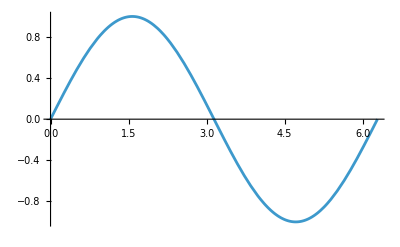

```mathematica
Plot[Sin[x],{x,0,2π}]
```

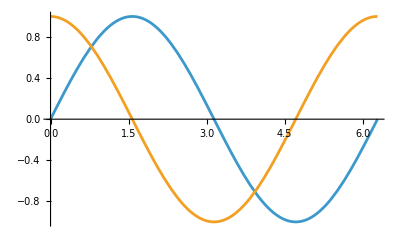

```mathematica
Plot[{Sin[x],Cos[x]},{x,0,2π}]
```

```mathematica
vysledok=Solve[x^2+2x-3==0,{x}]
```

{{x→-3},{x→1}}

```mathematica
?vysledok
```

```mathematica
funkcia[x_]:=x^2+2*x-3;
```

-Graphics-

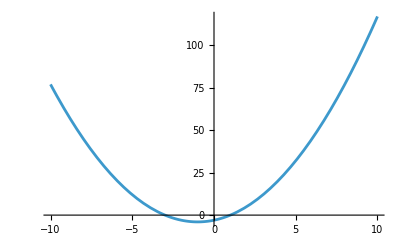

```mathematica
Plot[funkcia[b],{b,-10,10}]
```

```mathematica
list={1,a,funkcia[x],Sin[x],π}
list2={a,b,5}
list3=Union[{list,list2}]
Flatten[list3]
list3//MatrixForm
```

{1,a,-3+2 x+x^2==0,Sin[x],π}

{a,b,5}

{{a,b,5},{1,a,-3+2 x+x^2==0,Sin[x],π}}

{a,b,5,1,a,-3+2 x+x^2==0,Sin[x],π}

({a,b,5}
{1,a,-3+2 x+x^2==0,Sin[x],π})